```mathematica
Needs["ErrorBarPlots`"]
GenerateListOfFileNames[prefix_,date_,runtimes_]:=Module[{j,fileNames},
fileNames={};
For[j=1,j≤Length[runtimes],j++,
AppendTo[fileNames,StringJoin[prefix,date,"_",ToString[runtimes[[j]]],".dat"]]
];
fileNames
];
GetFileHeaderInfo[dataFileName_]:=Module[{rawFile,data,association,k},
rawFile=Import[dataFileName];
data={};
association=Association[];
k=1;
While[StringPart[rawFile[[k]][[1]],1]=="#",
association=Append[association,rawFile[[k]][[1]]->rawFile[[k]][[2]]];
k++;
];
association
];
GetFileDataset[dataFileName_]:=Module[{rawFile,headerStrippedData,columnHeaderLineNumber,lastColumnToImport,j,k,ass,tabularData,ds,rbAbsorptionRef,rbAbsorptionPro},
rawFile=Import[dataFileName];
k=1;

While[StringPart[rawFile[[k]][[1]],1]=="#",
k++;
];
headerStrippedData=Take[rawFile,{k,-1},All];
tabularData={};
For[j=2,j≤Length[headerStrippedData],j++,
If[Length[headerStrippedData[[j]]]>1,
ass=Association[];
For[k=1,k≤Length[headerStrippedData[[j]]],k++,
ass=Append[ass,headerStrippedData[[1]][[k]]->headerStrippedData[[j]][[k]]];
];
tabularData=Append[tabularData,ass];
]
];
ds =Dataset[tabularData]
];
ImportFile[dataFileName_]:={GetFileHeaderInfo[dataFileName],GetFileDataset[dataFileName]}
SetAttributes[GetFileDataset,Listable];
SetAttributes[GetFileHeaderInfo,Listable];
SetAttributes[ImportFile,Listable];

FourierFit[list_,rev_]:=Module[{fit,function,dataPts,stepSize,dataPtsPerRev,angles,data(*,C0,C2,C4,S2,S4*)},

function[θ_]= C0+C2 Cos[2(θ+θo)]+C4 Cos[4(θ+θo)]+S2 Sin[2(θ+θo)]+S4 Sin[4(θ+θo)];
dataPts=Length[list];
dataPtsPerRev=dataPts/rev;
angles=Range[0,(2π*rev)-2π/dataPtsPerRev,2π/dataPtsPerRev];
data=Transpose[{list,angles}];
fit=NonlinearModelFit[data,function[θ],{{C0,1000},C2,C4,S2,S4,θo},θ]
];


DFT[list_,rev_]:=Module[{numItems,i,k,j,reconstructionCos,reconstructionSin,returnCos,errorsCos,returnSin,errorsSin,intensity},
returnCos={};
errorsCos={};
returnSin={};
errorsSin={};
reconstructionCos={};
reconstructionSin={};
numItems=Length[list];

For[j=0,j<numItems/2,j++,
AppendTo[returnCos,0];
AppendTo[returnSin,0];

];

For[i=1,i<=numItems,i++,
intensity=list[[i]];
For [k=0,k<numItems/2,k++,
If[k==0 ||k==(numItems/2-1),
returnCos[[k+1]]=N[returnCos[[k+1]]+1/numItems*intensity*Cos[2*π *k *rev* (i-1)/numItems]];
returnSin[[k+1]]=N[returnSin[[k+1]]+1/numItems*intensity*Sin[2*π *k *rev* (i-1)/numItems]];,
returnCos[[k+1]]=N[returnCos[[k+1]]+2/numItems*intensity*Cos[2*π *k* rev *(i-1)/numItems]];
returnSin[[k+1]]=N[returnSin[[k+1]]+2/numItems*intensity*Sin[2*π *k* rev *(i-1)/numItems]];
];
];
];
(*

For[j=0,j<numItems/2,j++,
AppendTo[errorsSin,0];
AppendTo[errorsCos,0];
For[i=1,i<=numItems,i++,
intensity=list[[i]];
AppendTo[reconstructionCos,0];
AppendTo[reconstructionSin,0];
reconstructionCos[[i]]=intensity/Cos[2*π*j*rev*(i)/numItems] ;
If[j==0,reconstructionSin[[i]]=0,reconstructionSin[[i]]=intensity/Sin[2*π*1.0001*j*rev*(i)/numItems];];
For [k=0,k<numItems/2,k++,
If[k≠j,
reconstructionCos[[i]]-=(returnCos[[k+1]]*Cos[2*π*k*rev*(i)/numItems] +returnSin[[k+1]]*Sin[2*π*k*rev*(i)/numItems] )/Cos[2*π*j*rev*(i)/numItems];
If[j==0,reconstructionSin[[i]]=0,reconstructionSin[[i]]-=(returnCos[[k+1]]*Cos[2*π*k*rev*(i)/numItems] +returnSin[[k+1]]*Sin[2*π*k*rev*(1)/numItems] )/Sin[2*π*1.0001*j*rev*(i)/numItems]];
];
];
errorsSin[[j+1]]+=Power[reconstructionSin[[i]]-returnSin[[j+1]],2];
errorsCos[[j+1]]+=Power[reconstructionCos[[i]]-returnCos[[j+1]],2];
];
errorsSin[[j+1]]=Sqrt[errorsSin[[j+1]]/numItems];
errorsCos[[j+1]]=Sqrt[errorsCos[[j+1]]/numItems];
];
*)
{{returnSin,errorsSin},{returnCos,errorsCos}}
];

StokesParametersFromFourierData[intensityArray_,rev_,alpha_,beta0_,delta_]:=
Module[{fc(*Fourrier Coefficients*),c0,c2,c4,s2,s4,stokes},
fc=DFT[intensityArray,rev];
stokes={0,0,0,0,0,0};
c0=fc[[2]][[1]][[1]];
c2=fc[[2]][[1]][[3]];
c4=fc[[2]][[1]][[5]];
s2=fc[[1]][[1]][[3]];
s4=fc[[1]][[1]][[5]];
stokes[[1]]=c0-(1+Cos[delta])/(1-Cos[delta])*(c4*Cos[4 alpha+4 beta0]+s4*Sin[4 alpha+4 beta0]);
stokes[[2]]=2/(1-Cos[delta])*(c4*Cos[2alpha + 4 beta0]+s4*Sin[2alpha + 4 beta0])/stokes[[1]];
stokes[[3]]=2/(1-Cos[delta])*(s4*Cos[2alpha + 4 beta0]-c4*Sin[2alpha + 4 beta0])/stokes[[1]];
stokes[[4]]=Sqrt[c2^2+s2^2]/(Sin[delta]^2 stokes[[1]]);
stokes[[5]]=c2/(Sin[delta]Sin[2 alpha + 4 beta0]stokes[[1]]);
stokes[[6]]=-s2/(Sin[delta]Cos[2 alpha + 4 beta0]stokes[[1]]);
stokes

];
StokesParametersFromPolFile[polFile_,alpha_,beta0_,delta_]:=
Module[{intensityArray,f,rev},
f=ImportFile[polFile];
intensityArray=Normal[f[[2]][All,"COUNT"]];
rev=f[[1]]["#REV:"];
StokesParametersFromFourierData[intensityArray,rev,alpha,beta0,delta]
];

GetLinearPolarizationFraction[fileName_]:=Module[{data,angle,intensityArray,angleRAD,fc,intensity,linearPolarization,linearPolarizationFraction},
data=GetFileDataset[fileName];
intensityArray=Transpose[data][[2]];
fc=DFT[intensityArray,1] (*fc=fourier coefficients*);
intensity=fc[[2]][[1]];
linearPolarization=Sqrt[(fc[[2]][[3]])^2+(fc[[1]][[3]])^2];
linearPolarizationFraction=linearPolarization/intensity
];
SetAttributes[GetLinearPolarizationFraction,Listable];
GetAngle[fileName_]:=Module[{data,intensityArray,angleRAD,fc,intensity,linearPolarization,linearPolarizationFraction},
data=GetFileDataset[fileName];
intensityArray=Transpose[data][[2]];
fc=DFT[intensityArray,1] (*fc=fourier coefficients*);
.5*ArcTan[fc[[1]][[3]],fc[[2]][[3]]]
];
SetAttributes[GetAngle,Listable];

AverageDarkCountsRate[files_]:=Module[{i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
nDataPts=Length[Normal[files[[1]][[2]][All,"COUNT"]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell;
errorSum[[j]]+=counts[[j]]/nCycles^2*dwell^2;
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];
DarkCountsRate[files_]:=Module[{i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
nDataPts=Length[Normal[files[[1]][[2]][All,"COUNT"]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell;
errorSum[[j]]+=counts[[j]]/nCycles^2*dwell^2;
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

AverageBackgroundRateCurrentNorm[files_,darkCountsFiles_]:=Module[{darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
darkCountsRate=DarkCountsRate[darkCountsFiles];
nDataPts=Length[darkCountsRate[[1]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell/Abs[current[[j]]]-darkCountsRate[[1]][[j]]/nCycles/Abs[current[[j]]];
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*current[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*current[[j]]^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

BackgroundRateCurrentNorm[files_,darkCountsFiles_]:=Module[{darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
darkCountsRate=DarkCountsRate[darkCountsFiles];
nDataPts=Length[darkCountsRate[[1]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell/Abs[current[[j]]]-darkCountsRate[[1]][[j]]/nCycles/Abs[current[[j]]];
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*current[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*current[[j]]^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

AverageSignalRateCurrentNorm[files_,molyCountsRate_,darkCountsFiles_]:=Module[{darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,rev,j},
darkCountsRate=DarkCountsRate[darkCountsFiles];
nDataPts=Length[darkCountsRate[[1]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
rev=files[[i]][[1]]["#REV:"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/rev/dwell/Abs[current[[j]]]-darkCountsRate[[1]][[j]]/rev/nCycles/Abs[current[[j]]]-molyCountsRate[[1]][[j]]/rev/nCycles;
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*rev^2*current[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*rev^2*current[[j]]^2)-molyCountsRate[[2]][[j]]/(nCycles^2*rev^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

SignalRateCurrentNormFromFiles[file_,molyCountFiles_,darkCountsFiles_]:=Module[{molyCountsRate,darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
darkCountsRate=AverageDarkCountsRate[darkCountsFiles];
molyCountsRate=AverageBackgroundRateCurrentNorm[molyCountFiles,darkCountsFiles];
SignalRateCurrentNormFromRates[file,molyCountFiles,darkCountsFiles]
];

SignalRateCurrentNormFromRates[fileName_,molyCountsRate_,darkCountsRate_]:=Module[{file,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
file=ImportFile[fileName];
nDataPts=Length[Normal[file[[2]][All,"COUNT"]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
counts=Normal[file[[2]][All,"COUNT"]];
current=Normal[file[[2]][All,"CURRENT"]];
dwell=file[[1]]["#DWELL(s):"];
nCycles=file[[1]]["#REV:"];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell/Abs[current[[j]]]-darkCountsRate[[1]][[j]]/nCycles/Abs[current[[j]]]-molyCountsRate[[1]][[j]]/nCycles;
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*current[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*current[[j]]^2)-molyCountsRate[[2]][[j]]/(nCycles^2);
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

CalculateOneFileStokes[polFileName_,molyCountRate_,darkCountRate_,alpha_,beta_,delta_]:=Module[{signal,stokes,file,rev},
file=ImportFile[polFileName];
rev=file[[1]]["#REV:"];
signal=SignalRateCurrentNormFromRates[polFileName,molyCountRate,darkCountRate];
StokesParametersFromFourierData[signal[[1]],rev,alpha,beta,delta]
];

AverageStokes[stokesVectors_]:=Module[{transposedValues,stokes,stokesStdDev},
stokes=stokesVectors[[1]];
stokesStdDev=stokes;
transposedValues=Transpose[stokesVectors];
For[i=1,i≤Length[stokesVectors[[1]]],i++,
stokes[[i]]=Mean[transposedValues[[i]]];
stokesStdDev[[i]]=StandardDeviation[transposedValues[[i]]]/Sqrt[Length[transposedValues]];
];
{stokes,stokesStdDev}
];

CalculateAverageStokes[polFileNames_,molyCountRate_,darkCountRate_,alpha_,beta_,delta_]:=Module[{signal,stokes,stokesStdDev,file,rev,j,i,stokesValues,transposedValues},
stokes={0,0,0,0,0,0};
stokesStdDev={0,0,0,0,0,0};
stokesValues={};
For[j=1,j≤Length[polFileNames],j++,
stokes=CalculateOneFileStokes[polFileNames[[j]],molyCountRate,darkCountRate,alpha,beta,delta];
AppendTo[stokesValues,stokes]
];
AverageStokes[stokesValues];
]

NormalizeStokes[stokesVector_]:=Module[{intensity,newVector,i},
newVector=stokesVector;
intensity=stokesVector[[1]];
For[i=2,i≤Length[stokesVector],i++,
newVector[[i]]=stokesVector[[i]]/intensity;
];
newVector
];

UnNormalizeStokes[stokesVector_]:=Module[{intensity,newVector,i},
newVector=stokesVector;
intensity=stokesVector[[1]];
For[i=2,i≤Length[stokesVector],i++,
newVector[[i]]=stokesVector[[i]]*intensity;
];
newVector
];

SubtractStokes[addedStokes_,subtractedStokes_]:=Module[
{unNormAdd,unNormSub},
unNormAdd=UnNormalizeStokes[addedStokes];
unNormSub=UnNormalizeStokes[subtractedStokes];
NormalizeStokes[unNormAdd-unNormSub]
];
```

```mathematica
raspberryPi=FileNameJoin[{"Z:","RbData","2017-12-20"}];
dropBoxfolder=FileNameJoin[{"C:","Users","kahrendsen2","Dropbox"}];
dataFolder=FileNameJoin[{"00School","research","DataRuns"}];
folder=FileNameJoin[{dropBoxfolder,dataFolder}];
SetDirectory[folder];
FileNames[]
```

{15-06-09_USBCounterError,15-07-06mockPolarizationData,16-01-14,16-01-21_Data,16-05-25_PolarizationData,16-07-06_PolarizationData,16-08-04_PolarizationData,16-08-07_HeliumTargetPictures,16-08-09_PolarizationData,16-10-17_polarimeter,16-10-27_DataReport,16-11-03_faradayRotation,16-11-07_faradayRotation,16-11-18_faradayRotation,16-12-09_faradayRotation,17-01-31,17-02-17_plusMinus,17-03-06_PlusMinusWavemeter,17-03-10_non-RbFaradayRotation,17-03-15_AimingFor5e12,17-03-15_wavemeterNoRb,17-03-28,17-03-29_pumpLaserFindingCircular,17-03-30_WavemeterReliability,17-04-04_polarization,17-04-06_polarization,17-04-07_wmReliability,17-04-18,17-04-18_polarization,17-04-22,17-04-25_ProbePolarizationDriftOpenChamber,17-04-30_laserReport,17-05-17_DirtyGunRun,17-05-18_ProbeDrift,17-05-19_BetterLaser,17-05-24_SimplifiedPolarization,17-05-25_LaserProfiling,17-06-02,17-06-06_IntensityOfProbeStudy,17-06-11,17-06-13,17-06-16,17-06-17,17-06-25,17-07-01_nRbVsBufferGasAnalysis,17-07-01_PumpLaserAnalysis,17-07-03_lowerNRb_BGPStudy,17-07-03_ProbeDrift,17-07-03_pumpBroadening,17-07-06_lotsOfProbeMeasurements,17-07-06_MagneticField,17-07-06_probePower,17-07-12_polVsPumpPower,17-08-01_rgaInitialScans,17-08-03_redoingSystemDiagnostic,17-08-06_probeDrift,17-08-18_furtherPolarizationStudy,17-08-19_furtherPolarizationStudy2,17-08-22_furtherPolarizationStudyFoundLeak,17-08-29_BvsProbePower_probeDetuneVsMagnetRot,17-09-05_Polarizations_100mTBGP,17-09-20,17-10-03_ElectronGun,17-10-16_ElectronGun,17-10-24_UnpolarizedPolarization,17-10-26_24And30eVRuns,17-10-28_24and30eVRedux,17-11-04_MoreUnpolarizedRuns,17-11-06_UnpolarizedRuns2,17-11-15_BalancedPhotoDetector,17-11-18_SystemDiagnosis,17-12-18_SystemDiagnosis,17-12-20_PolarizingElectrons,18-01-03_PolarizingElectrons,NewFile2.tsv,NewFile.tsv,pumpPower.png}

```mathematica
SetDirectory[FileNameJoin[{folder,"18-01-03_PolarizingElectrons"}]];
names=FileNames[StringExpression["POL",__,"_",__,DigitCharacter,".dat"]]
darkFileNames=Take[names,{2,6}];
darkFiles=ImportFile[darkFileNames]; (* A "File" here means a list consisting of two elements. The first element is a list of associations containing information pertinent to all of the datapoints, the "header." The second element is the dataset.*)
darkCounts=N[DarkCountsRate[darkFiles]](*DarkCountsRate takes as an argument a list of "files" as defined above, and returns two lists. The first list is the average dark count at each polarimeter position. The second list is the standard deviation of that countRate, as per Clayburn's thesis.*)
```

{POL2018-01-03_093839.dat,POL2018-01-03_120212.dat,POL2018-01-03_120532.dat,POL2018-01-03_120852.dat,POL2018-01-03_121211.dat,POL2018-01-03_121531.dat,POL2018-01-03_122503.dat,POL2018-01-03_122822.dat,POL2018-01-03_123142.dat,POL2018-01-03_123502.dat,POL2018-01-03_123822.dat,POL2018-01-03_125059.dat,POL2018-01-03_125418.dat,POL2018-01-03_125738.dat,POL2018-01-03_130058.dat,POL2018-01-03_130418.dat}

{{40.8,46.7333,48.2,48.2,54.8,45.2667,50.2667,45.6,45.8,46.0667,44.5333,43.4,47.6,42.3333,43.1333,46.3333,41.8667,45.1333,44.6,47.4667,49.8667,49.2,47.7333,44.0667,45.2667,42.2,42.4,42.1333,41.2667,42.4667,45.2,44.6,51.4,45.6667,48.8667,51.2,45.8,45.6667,48.5333,43.4667,44.6,40.6667,42.4667,41.,40.4,42.,46.5333,42.1333,48.8667,50.2,50.,48.7333,47.4667,42.4,43.3333,44.8,41.8667,42.9333,42.9333,43.5333},{14.8432,15.8858,16.1332,16.1332,17.2023,15.6346,16.4754,15.692,15.7264,15.7721,15.5074,15.3088,16.0325,15.1195,15.2617,15.8177,15.036,15.6115,15.519,16.01,16.4098,16.2997,16.0549,15.426,15.6346,15.0957,15.1314,15.0838,14.9278,15.1433,15.6231,15.519,16.6601,15.7035,16.2444,16.6277,15.7264,15.7035,16.1889,15.3206,15.519,14.8189,15.1433,14.8795,14.7702,15.0599,15.8518,15.0838,16.2444,16.4645,16.4317,16.2222,16.01,15.1314,15.2971,15.5538,15.036,15.2263,15.2263,15.3323}}

```mathematica
StokesParametersFromFourierData[darkCounts[[1]],1,20.4*Pi/180,63.3*Pi/180,90*Pi/180]
```

```mathematica
SetDirectory[FileNameJoin[{folder,"17-12-20_PolarizingElectrons","unpolarizedElectrons"}]];
names=FileNames[StringExpression["POL",__,"_",__,DigitCharacter,".dat"]];

runs=10;
energies={30};
energyXdarkFileNames={};
For[i=1,i≤Length[energies],i++,
fileNames=Take[names,{i+0,Length[energies]*runs,Length[energies]}];
AppendTo[energyXdarkFileNames,fileNames];
];

averagedDark={};
energyXdarkFiles={};

For[j=1,j≤Length[energyXdarkFileNames],j++,
files=ImportFile[energyXdarkFileNames[[j]]];
AppendTo[energyXdarkFiles,files];
(* A "File" here means a list consisting of two elements. The first element is a list of associations containing information pertinent to all of the datapoints, the "header." The second element is the dataset.*)
averageDark=N[DarkCountsRate[files]];
AppendTo[averagedDark,averageDark];
];

averagedDark
```

{{{53.3,52.74,51.84,53.46,53.96,53.26,52.12,53.52,54.02,52.82,52.74,49.18,52.48,49.6,54.12,53.54,52.12,55.9,52.36,51.82,53.1,52.44,52.02,53.9,51.74,52.06,51.,52.5,52.48,53.06,51.94,52.36,53.68,55.02,53.14,55.46,51.12,53.98,51.46,52.78,53.5,52.68,53.88,52.,53.78,53.62,52.96,53.44,53.86,52.64,50.7,54.58,53.38,52.02,52.64,52.04,51.66,52.82,52.92,53.62},{25.8118,25.6759,25.4558,25.8505,25.9711,25.8021,25.5245,25.865,25.9856,25.6953,25.6759,24.7942,25.6125,24.8998,26.0096,25.8699,25.5245,26.4339,25.5832,25.4509,25.7633,25.6027,25.5,25.9567,25.4313,25.5098,25.2488,25.6174,25.6125,25.7536,25.4804,25.5832,25.9037,26.225,25.773,26.3296,25.2784,25.976,25.3624,25.6856,25.8602,25.6613,25.9519,25.4951,25.9278,25.8892,25.7294,25.8457,25.9471,25.6515,25.1744,26.1199,25.8312,25.5,25.6515,25.5049,25.4116,25.6953,25.7196,25.8892}}}

```mathematica
SetDirectory[FileNameJoin[{folder,"17-11-06_UnpolarizedRuns2"}]];
names=FileNames[StringExpression["POL",__,"_",__,DigitCharacter,".dat"]];


runs=10;
energies={30,27,24,23,22,16};
energyXmolyFileNames={};
energyXsignalFileNames={};
For[i=1,i≤Length[energies],i++,
molyFileNames=Take[names,{(i+Length[energies]*runs),(2*Length[energies]*runs),(Length[energies])}];
signalFileNames=Take[names,{i+0,Length[energies]*runs,Length[energies]}];
AppendTo[energyXmolyFileNames,molyFileNames];
AppendTo[energyXsignalFileNames,signalFileNames];
];

energyXmolyFileNames
```

{{POL2017-11-08_092806.dat,POL2017-11-08_100706.dat,POL2017-11-08_104606.dat,POL2017-11-08_112507.dat,POL2017-11-08_120407.dat,POL2017-11-08_124310.dat,POL2017-11-08_132210.dat,POL2017-11-08_140111.dat,POL2017-11-08_144011.dat,POL2017-11-08_151912.dat},{POL2017-11-08_093436.dat,POL2017-11-08_101336.dat,POL2017-11-08_105237.dat,POL2017-11-08_113137.dat,POL2017-11-08_121037.dat,POL2017-11-08_124940.dat,POL2017-11-08_132840.dat,POL2017-11-08_140741.dat,POL2017-11-08_144641.dat,POL2017-11-08_152542.dat},{POL2017-11-08_094106.dat,POL2017-11-08_102006.dat,POL2017-11-08_105907.dat,POL2017-11-08_113807.dat,POL2017-11-08_121707.dat,POL2017-11-08_125610.dat,POL2017-11-08_133511.dat,POL2017-11-08_141411.dat,POL2017-11-08_145311.dat,POL2017-11-08_153212.dat},{POL2017-11-08_094736.dat,POL2017-11-08_102636.dat,POL2017-11-08_110537.dat,POL2017-11-08_114437.dat,POL2017-11-08_122338.dat,POL2017-11-08_130240.dat,POL2017-11-08_134141.dat,POL2017-11-08_142041.dat,POL2017-11-08_145941.dat,POL2017-11-08_153842.dat},{POL2017-11-08_095406.dat,POL2017-11-08_103306.dat,POL2017-11-08_111207.dat,POL2017-11-08_115107.dat,POL2017-11-08_123008.dat,POL2017-11-08_130910.dat,POL2017-11-08_134811.dat,POL2017-11-08_142711.dat,POL2017-11-08_150611.dat,POL2017-11-08_154512.dat},{POL2017-11-08_100036.dat,POL2017-11-08_103936.dat,POL2017-11-08_111837.dat,POL2017-11-08_115737.dat,POL2017-11-08_123638.dat,POL2017-11-08_131540.dat,POL2017-11-08_135441.dat,POL2017-11-08_143341.dat,POL2017-11-08_151241.dat,POL2017-11-08_155142.dat}}

```mathematica
averagedMolyDarkSubtracted={};

For[j=1,j≤Length[energyXmolyFileNames],j++,
files=ImportFile[energyXmolyFileNames[[j]]];
averageMolyDarkSubtracted=N[AverageBackgroundRateCurrentNorm[files,darkFilesLightsOn]];
AppendTo[averagedMolyDarkSubtracted,averageMolyDarkSubtracted];
];
averagedMolyDarkSubtracted
```

{{{35.8906,51.7688,43.2124,19.5515,40.1122,38.7375,34.5244,28.8193,24.2211,46.736,26.4248,19.9413,38.262,27.1014,40.1408,30.2023,25.085,34.2265,32.953,42.3847,26.3637,39.3303,24.0006,25.7177,26.9857,41.3279,42.9586,26.5335,40.2965,32.3096,44.5922,34.09,38.6178,35.2111,19.6585,2.62303,43.5951,39.4892,26.3423,24.9477,35.8713,40.0801,20.0996,32.1262,40.0884,46.9002,31.6351,36.7927,31.9429,37.9345,43.9039,47.4735,26.0842,26.5189,45.0597,24.7906,32.0044,43.5491,28.7336,27.8359},{1.29675,1.33004,1.31972,1.23543,1.3167,1.33486,1.30849,1.29215,1.25599,1.29645,1.23222,1.18364,1.23265,1.23742,1.2935,1.24843,1.2347,1.28134,1.27153,1.32136,1.26278,1.3256,1.2334,1.22133,1.21654,1.26099,1.24185,1.19553,1.25103,1.2155,1.27422,1.23462,1.28714,1.2581,1.21098,1.16642,1.27397,1.2887,1.23496,1.20758,1.24931,1.25138,1.17403,1.20221,1.26789,1.2869,1.21895,1.26384,1.26317,1.2873,1.30576,1.33122,1.22716,1.21997,1.28226,1.21014,1.20442,1.24158,1.20865,1.2179}},{{27.9953,44.7833,34.8959,16.2593,36.9864,28.4439,27.3494,21.3517,18.2261,42.5096,16.8636,14.2399,35.4903,16.4938,31.2747,24.3072,20.4358,27.913,27.8597,35.1847,18.8199,31.1061,18.8509,21.9847,22.5788,33.9165,38.5184,20.6979,32.0433,23.7626,39.2769,29.5743,29.215,30.1346,19.2562,-0.625862,43.4383,36.1521,17.7731,17.7435,25.0298,34.2801,10.5793,24.1819,29.8794,35.6187,27.273,31.3345,26.0649,30.5244,39.4099,38.3678,21.8852,22.8986,39.8111,13.9669,27.5897,39.1805,25.8057,22.3832},{1.18722,1.23863,1.20864,1.1676,1.2578,1.20304,1.20861,1.18841,1.17018,1.23748,1.10965,1.10265,1.18394,1.09503,1.17864,1.16142,1.15971,1.19739,1.19674,1.2339,1.16483,1.2257,1.16373,1.16957,1.15543,1.17332,1.18921,1.12432,1.15649,1.11694,1.21508,1.18499,1.18679,1.20454,1.20432,1.12341,1.26891,1.24869,1.13214,1.11982,1.12348,1.18078,1.05326,1.10693,1.15027,1.1637,1.16707,1.19957,1.19651,1.20176,1.25172,1.23231,1.17674,1.17328,1.22137,1.08166,1.14735,1.18971,1.17135,1.14825}},{{18.7496,37.8231,28.759,11.7096,27.4203,22.9558,20.2315,11.4908,8.38546,33.6943,12.2385,7.6356,28.432,12.2533,24.988,17.0057,13.0853,19.4535,23.8817,30.9659,14.4375,20.4671,11.5489,14.9616,19.0039,27.987,31.1459,12.7487,28.8122,25.252,32.392,24.0218,24.684,26.7195,11.6315,-2.96166,35.7566,23.893,14.1743,15.0178,25.1165,26.6928,9.4878,19.1212,25.3446,33.7649,20.0804,27.8864,18.791,24.1816,33.3826,34.1226,17.0691,14.2115,31.6884,10.2344,25.0397,31.9274,16.1155,15.6605},{1.07515,1.15696,1.13414,1.11294,1.15203,1.13466,1.11924,1.06716,1.04456,1.13384,1.04571,1.01323,1.09935,1.03525,1.10012,1.06735,1.06642,1.08891,1.148,1.17986,1.10804,1.10315,1.07441,1.08316,1.10939,1.10024,1.1014,1.02398,1.11422,1.12783,1.13253,1.11343,1.12404,1.15599,1.1043,1.08482,1.18294,1.10682,1.08639,1.08153,1.12001,1.08793,1.03226,1.04033,1.09225,1.13651,1.07774,1.15545,1.1051,1.1225,1.17972,1.17908,1.10885,1.06278,1.12076,1.02866,1.10932,1.09975,1.04658,1.05902}},{{19.2798,37.0574,25.441,9.49626,25.5342,22.7007,20.1946,10.0765,8.86354,32.79,12.4961,7.58277,24.4445,11.8854,21.5496,15.5723,11.503,16.3409,18.1531,24.4144,12.881,23.0903,12.3106,12.3965,14.2545,24.1183,27.8045,10.0029,24.4294,16.85,31.7285,19.6463,23.8897,26.6599,7.85537,-6.81396,35.4665,27.481,13.9783,10.8148,18.4755,26.3686,3.51538,19.1629,23.6961,31.0727,19.097,21.0831,17.0692,24.6101,26.5812,30.6612,12.2892,12.364,30.55,9.80115,18.7626,31.6213,14.671,12.6349},{1.07206,1.14473,1.08926,1.07555,1.11972,1.12187,1.11002,1.04099,1.04198,1.11345,1.03904,1.00941,1.05172,1.03771,1.07177,1.07599,1.08014,1.08216,1.1129,1.13235,1.11673,1.15668,1.1178,1.07828,1.07377,1.06787,1.0824,1.00605,1.08096,1.04252,1.14727,1.08221,1.13828,1.18032,1.08473,1.06401,1.19795,1.1628,1.09615,1.04937,1.05379,1.09642,0.966554,1.05062,1.0808,1.10741,1.06665,1.07697,1.08181,1.12576,1.09986,1.13595,1.04597,1.03067,1.1026,1.01812,1.03103,1.09566,1.02633,1.02697}},{{17.2882,35.6718,24.9075,8.87754,26.2555,19.4232,15.0398,10.1634,7.10304,28.5454,9.12895,3.02274,21.1225,9.16112,19.7997,12.7323,9.84531,14.1233,15.9564,30.2612,9.06188,18.9265,7.46195,12.4674,12.8578,27.49,27.8976,10.8119,22.6373,17.6804,29.9961,17.6707,21.2853,22.4104,10.8104,-11.5886,32.6844,23.5541,5.26856,9.4593,16.2768,20.2251,4.8023,17.0579,24.6392,33.882,18.3855,19.8935,11.5478,22.664,25.9552,31.2208,12.0771,12.6742,29.4587,3.73842,17.6497,31.9975,11.4111,11.0659},{1.06726,1.15998,1.12195,1.13529,1.19103,1.14916,1.10941,1.10749,1.08369,1.11532,1.06048,1.00541,1.05829,1.0497,1.08087,1.0629,1.0725,1.06681,1.09583,1.20982,1.08579,1.12772,1.05847,1.07761,1.06224,1.11047,1.08073,1.02007,1.065,1.08128,1.15247,1.08846,1.13254,1.15584,1.14992,1.0343,1.18486,1.13952,1.01001,1.05787,1.04957,1.04596,1.01518,1.05254,1.11793,1.17549,1.09529,1.1139,1.07945,1.16947,1.15974,1.20115,1.12553,1.10563,1.1495,1.00472,1.07518,1.15358,1.04656,1.06603}},{{15.7136,32.8905,27.6389,8.48428,29.0217,21.8829,17.3833,11.8176,9.32735,30.5417,5.71844,8.75883,26.7833,10.8188,21.9148,12.387,9.71048,20.1714,19.6038,28.6078,12.8881,21.0865,9.98826,9.52256,11.8746,25.1368,31.3943,12.8654,25.5113,16.7981,35.7589,22.8721,20.9849,23.1826,7.63155,-7.51406,37.2723,24.8984,10.2779,9.64236,20.4171,25.0481,7.42564,18.1192,21.2012,31.4158,21.5922,25.4807,20.6328,24.6142,31.1206,30.0702,13.5914,14.4946,31.8933,7.27723,18.4373,31.87,14.4031,13.3527},{1.09488,1.14535,1.17268,1.12916,1.20929,1.16581,1.13047,1.11152,1.09103,1.12091,0.983678,1.05007,1.09717,1.04141,1.08669,1.0417,1.0686,1.14666,1.14727,1.2037,1.14396,1.16163,1.10932,1.07073,1.07469,1.11145,1.14544,1.06708,1.11726,1.06794,1.21565,1.14014,1.13039,1.16111,1.10608,1.09022,1.23659,1.16248,1.08265,1.05807,1.10192,1.10261,1.0445,1.05993,1.06909,1.13279,1.1199,1.15348,1.15192,1.15225,1.17732,1.15461,1.09393,1.09131,1.1457,1.01513,1.05271,1.12269,1.05143,1.05795}}}

```mathematica
averagedSignalBackgroundSubtracted={};


For[j=1,j≤Length[energyXsignalFileNames],j++,
files=ImportFile[energyXsignalFileNames[[j]]];
averageSignalBackgroundSubtracted=N[AverageSignalRateCurrentNorm[files,averagedMolyDarkSubtracted[[j]],energyXdarkFiles[[j]]]];
AppendTo[averagedSignalBackgroundSubtracted,averageSignalBackgroundSubtracted];
];
averagedSignalBackgroundSubtracted
```

{{{819.759,801.049,807.679,820.45,782.859,784.437,793.189,788.558,822.772,799.333,826.062,853.594,833.81,849.833,809.185,825.575,816.968,795.342,794.734,789.987,794.411,775.394,799.366,815.468,815.08,808.762,815.692,831.2,822.362,829.999,819.705,820.461,803.446,790.549,807.755,811.861,779.901,789.645,809.053,812.208,812.92,823.491,839.493,833.618,825.923,810.824,816.766,791.821,798.985,779.405,766.314,771.577,795.776,808.829,804.819,821.259,828.214,825.142,844.376,833.665},{4.04212,3.97287,3.93034,3.95819,3.79595,3.77207,3.91541,3.81851,3.97005,3.95291,3.98608,4.00914,4.04805,4.06615,3.90065,3.96919,3.96334,3.80062,3.8486,3.93264,3.89418,3.88813,3.87994,3.99045,3.95039,4.0024,3.98952,3.98449,3.96008,4.0623,4.07247,3.93886,3.87626,3.86556,3.92701,3.85908,3.89321,3.86214,3.90013,3.87309,3.95299,4.04224,3.95288,4.05875,4.04904,4.00145,4.02065,3.7985,3.89818,3.81874,3.77203,3.86186,3.95715,3.90486,4.00102,3.94286,4.10021,4.06913,4.07116,4.03656}},{{739.905,721.956,713.172,744.976,710.486,723.574,712.502,723.029,725.464,710.071,743.693,745.635,739.028,752.023,736.265,729.312,732.728,712.806,703.229,703.31,717.471,701.875,716.821,720.355,721.201,718.382,726.821,753.761,748.438,747.773,717.98,729.419,719.463,718.304,723.088,735.184,693.672,698.477,732.367,741.164,727.962,732.204,753.774,749.804,736.782,728.119,730.981,708.997,726.651,707.365,688.115,700.866,717.578,718.287,701.934,747.828,739.128,731.69,746.732,740.017},{3.71498,3.63128,3.59249,3.72316,3.61361,3.70302,3.56532,3.57386,3.58449,3.59686,3.6539,3.57402,3.71727,3.61018,3.66382,3.63409,3.63608,3.46477,3.45719,3.60399,3.52043,3.47352,3.47748,3.62318,3.47979,3.60426,3.69506,3.69053,3.6896,3.67685,3.55351,3.63408,3.54199,3.53416,3.54059,3.54425,3.49643,3.48752,3.57904,3.62266,3.63623,3.71779,3.6644,3.64083,3.62233,3.66702,3.58283,3.49117,3.6836,3.50162,3.49821,3.52299,3.49613,3.50071,3.49087,3.68688,3.61438,3.68758,3.70302,3.58817}},{{227.2,208.069,215.081,228.92,212.078,220.747,217.945,235.291,238.988,216.517,235.119,234.864,218.998,241.152,218.811,221.764,227.328,224.893,212.893,204.85,228.968,225.012,231.85,226.572,217.724,226.654,213.58,230.897,214.292,217.904,214.12,219.545,217.169,209.003,225.748,240.734,204.914,214.661,224.259,231.641,223.309,224.675,231.743,226.208,223.174,213.582,231.384,210.877,225.48,213.41,204.675,203.759,224.682,225.691,208.796,233.847,226.655,213.648,230.306,225.578},{0.+1.06321 ⅈ,0.+0.999759 ⅈ,0.+1.17054 ⅈ,0.+1.07977 ⅈ,0.+1.19776 ⅈ,0.+0.871459 ⅈ,0.+1.31477 ⅈ,0.+0.656944 ⅈ,0.+0.71887 ⅈ,0.+0.81366 ⅈ,0.+0.995095 ⅈ,0.+1.2535 ⅈ,0.+1.08054 ⅈ,0.+0.574795 ⅈ,0.+1.05631 ⅈ,0.+1.32856 ⅈ,0.+1.22782 ⅈ,0.+1.34566 ⅈ,0.+1.2082 ⅈ,0.+1.33974 ⅈ,0.+1.07575 ⅈ,0.+0.866492 ⅈ,0.+1.14844 ⅈ,0.+1.33427 ⅈ,0.+1.31197 ⅈ,0.+0.396926 ⅈ,0.+0.910824 ⅈ,0.+1.1461 ⅈ,0.+1.28247 ⅈ,0.+1.22045 ⅈ,0.+0.996664 ⅈ,0.+1.20882 ⅈ,0.+1.10848 ⅈ,0.+1.40116 ⅈ,0.+1.19825 ⅈ,0.+1.09499 ⅈ,0.+0.879346 ⅈ,0.+1.24289 ⅈ,0.+1.10343 ⅈ,0.+0.939955 ⅈ,0.+0.924969 ⅈ,0.+0.935763 ⅈ,0.+1.11525 ⅈ,0.+0.974687 ⅈ,0.+0.951953 ⅈ,0.+1.02719 ⅈ,0.+1.01838 ⅈ,0.+1.23828 ⅈ,0.+1.02478 ⅈ,0.+1.14504 ⅈ,0.+1.32084 ⅈ,0.+1.22528 ⅈ,0.+1.05309 ⅈ,0.+1.2748 ⅈ,0.+1.353 ⅈ,0.+1.16774 ⅈ,0.+1.01152 ⅈ,0.+1.10016 ⅈ,0.+1.0838 ⅈ,0.+1.4781 ⅈ}},{{29.2264,12.9813,24.4004,36.6684,25.7596,22.5175,23.6378,35.0073,35.2238,11.9219,30.9018,36.3792,17.4269,34.1296,19.4652,26.5617,30.3042,28.5925,24.9842,17.2938,22.6154,25.7572,29.1425,31.098,32.8886,21.2488,17.0835,34.3915,18.8517,27.4923,8.73282,26.2043,19.9859,22.8296,32.0498,51.7144,5.11167,15.5439,26.1742,29.9779,26.5609,16.7876,35.3554,26.2532,17.432,8.88954,20.2034,24.7622,23.9018,18.6797,12.0452,13.3057,27.7145,31.7961,13.3811,35.1948,20.2458,5.94212,27.1015,28.6252},{0.+2.62938 ⅈ,0.+2.62841 ⅈ,0.+2.65592 ⅈ,0.+2.66317 ⅈ,0.+2.52932 ⅈ,0.+2.57889 ⅈ,0.+2.63336 ⅈ,0.+2.573 ⅈ,0.+2.61587 ⅈ,0.+2.54439 ⅈ,0.+2.65193 ⅈ,0.+2.59115 ⅈ,0.+2.69159 ⅈ,0.+2.60909 ⅈ,0.+2.74494 ⅈ,0.+2.65541 ⅈ,0.+2.62062 ⅈ,0.+2.65649 ⅈ,0.+2.58799 ⅈ,0.+2.73551 ⅈ,0.+2.85503 ⅈ,0.+2.59204 ⅈ,0.+2.69023 ⅈ,0.+2.6277 ⅈ,0.+2.48634 ⅈ,0.+2.53803 ⅈ,0.+2.61942 ⅈ,0.+2.58829 ⅈ,0.+2.69152 ⅈ,0.+2.60202 ⅈ,0.+2.69608 ⅈ,0.+2.60798 ⅈ,0.+2.65242 ⅈ,0.+2.50007 ⅈ,0.+2.77955 ⅈ,0.+2.54595 ⅈ,0.+2.68868 ⅈ,0.+2.61805 ⅈ,0.+2.67877 ⅈ,0.+2.72067 ⅈ,0.+2.55051 ⅈ,0.+2.66841 ⅈ,0.+2.72616 ⅈ,0.+2.54161 ⅈ,0.+2.68278 ⅈ,0.+2.71787 ⅈ,0.+2.76331 ⅈ,0.+2.57991 ⅈ,0.+2.74256 ⅈ,0.+2.66117 ⅈ,0.+2.67944 ⅈ,0.+2.57689 ⅈ,0.+2.67011 ⅈ,0.+2.5651 ⅈ,0.+2.57443 ⅈ,0.+2.51731 ⅈ,0.+2.73521 ⅈ,0.+2.76357 ⅈ,0.+2.60806 ⅈ,0.+2.71401 ⅈ}},{{5.36022,-11.4585,-0.292667,16.0156,-0.404245,2.05989,12.431,9.60839,16.9551,-4.79115,18.1516,22.3944,6.4394,14.9446,7.19466,14.895,11.8439,8.68158,4.47774,-2.20224,13.0302,10.0929,19.2113,12.8997,17.8611,-3.56917,-3.3091,13.8812,-2.43559,5.12037,-2.73345,6.06669,2.5811,5.42273,11.3403,34.2914,-8.86703,-3.53336,13.5473,15.7667,6.85204,2.19763,19.4323,3.61925,-0.889119,-10.7941,4.91888,4.70096,11.8451,4.94131,-3.7591,-3.07638,10.8924,12.6412,-2.89166,19.7775,0.592768,-8.88026,17.3406,12.9065},{0.+2.77931 ⅈ,0.+2.74279 ⅈ,0.+2.75356 ⅈ,0.+2.68 ⅈ,0.+2.69029 ⅈ,0.+2.78093 ⅈ,0.+2.63722 ⅈ,0.+2.8721 ⅈ,0.+2.7555 ⅈ,0.+2.74398 ⅈ,0.+2.58932 ⅈ,0.+2.65601 ⅈ,0.+2.68149 ⅈ,0.+2.7476 ⅈ,0.+2.56688 ⅈ,0.+2.62082 ⅈ,0.+2.81635 ⅈ,0.+2.76217 ⅈ,0.+2.87993 ⅈ,0.+2.64056 ⅈ,0.+2.81058 ⅈ,0.+2.62768 ⅈ,0.+2.68612 ⅈ,0.+2.70386 ⅈ,0.+2.54166 ⅈ,0.+2.74218 ⅈ,0.+2.67884 ⅈ,0.+2.77364 ⅈ,0.+2.88592 ⅈ,0.+2.78381 ⅈ,0.+2.63571 ⅈ,0.+2.78574 ⅈ,0.+2.75092 ⅈ,0.+2.69638 ⅈ,0.+2.77229 ⅈ,0.+2.80395 ⅈ,0.+2.76313 ⅈ,0.+2.86135 ⅈ,0.+2.89013 ⅈ,0.+2.72816 ⅈ,0.+2.81237 ⅈ,0.+2.76505 ⅈ,0.+2.7543 ⅈ,0.+2.78032 ⅈ,0.+2.75457 ⅈ,0.+2.71584 ⅈ,0.+2.77527 ⅈ,0.+2.80228 ⅈ,0.+2.78119 ⅈ,0.+2.70201 ⅈ,0.+2.82316 ⅈ,0.+2.56493 ⅈ,0.+2.84188 ⅈ,0.+2.67169 ⅈ,0.+2.64252 ⅈ,0.+2.67724 ⅈ,0.+2.81803 ⅈ,0.+2.72963 ⅈ,0.+2.63696 ⅈ,0.+2.70161 ⅈ}},{{5.06794,-9.67605,-4.75484,13.2798,-5.61621,0.350561,4.74344,11.9295,13.7111,-8.05161,18.3155,14.7378,-4.84918,10.7914,-0.150516,12.0327,13.5234,0.674833,4.29029,-7.30528,10.9412,7.05813,13.818,13.4746,12.4014,-0.0262255,-7.77177,7.66868,-1.8778,5.07735,-9.97796,2.02415,2.10009,-0.673653,18.0412,29.8333,-13.758,-2.04778,13.5182,20.212,1.24901,-0.0923481,17.1402,4.25972,6.25731,-5.39895,4.99899,-1.49878,2.12581,-2.34719,-6.32922,-9.06064,5.51711,8.41211,-9.90347,15.8688,5.53158,-10.06,9.50788,10.8347},{0.+2.82903 ⅈ,0.+2.79204 ⅈ,0.+2.79202 ⅈ,0.+2.82646 ⅈ,0.+2.7369 ⅈ,0.+2.80556 ⅈ,0.+2.7794 ⅈ,0.+2.77507 ⅈ,0.+2.6848 ⅈ,0.+2.75361 ⅈ,0.+2.73436 ⅈ,0.+2.77213 ⅈ,0.+2.80551 ⅈ,0.+2.8017 ⅈ,0.+2.8194 ⅈ,0.+2.69081 ⅈ,0.+2.73552 ⅈ,0.+2.85309 ⅈ,0.+2.66799 ⅈ,0.+2.87328 ⅈ,0.+2.86357 ⅈ,0.+2.62573 ⅈ,0.+2.78359 ⅈ,0.+2.81643 ⅈ,0.+2.72922 ⅈ,0.+2.69981 ⅈ,0.+2.84637 ⅈ,0.+2.86373 ⅈ,0.+2.77682 ⅈ,0.+2.77902 ⅈ,0.+2.72521 ⅈ,0.+2.75336 ⅈ,0.+2.70181 ⅈ,0.+2.86142 ⅈ,0.+2.75391 ⅈ,0.+2.8314 ⅈ,0.+2.76836 ⅈ,0.+2.70457 ⅈ,0.+2.7394 ⅈ,0.+2.54163 ⅈ,0.+2.87169 ⅈ,0.+2.67951 ⅈ,0.+2.7391 ⅈ,0.+2.69996 ⅈ,0.+2.63983 ⅈ,0.+2.73705 ⅈ,0.+2.70414 ⅈ,0.+2.84824 ⅈ,0.+2.795 ⅈ,0.+2.89832 ⅈ,0.+2.76807 ⅈ,0.+2.81493 ⅈ,0.+2.90851 ⅈ,0.+2.77827 ⅈ,0.+2.79483 ⅈ,0.+2.80321 ⅈ,0.+2.71959 ⅈ,0.+2.78504 ⅈ,0.+2.61781 ⅈ,0.+2.73645 ⅈ}}}

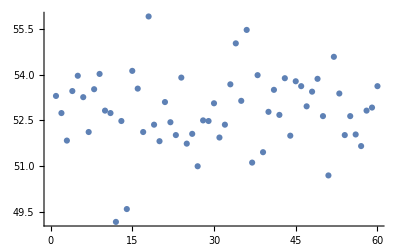

```mathematica
darkPlotData={};
molyPlotData={};
signalPlotData={};
For[i=1,i≤Length[energies],i++,
AppendTo[darkPlotData,averagedDark[[i]][[1]]];
(*AppendTo[molyPlotData,averagedMolyDarkSubtracted[[i]][[1]]];
AppendTo[signalPlotData,averagedSignalBackgroundSubtracted[[i]][[1]]];*)
];
darkPlots=ListPlot[darkPlotData];
(*molyPlots=ListPlot[molyPlotData];
signalPlots=ListPlot[signalPlotData];*)
GraphicsGrid[{{darkPlots},{molyPlots},{signalPlots}}]
```

```mathematica
alphaOld=3.2*π/180;
betaOld=-6.95*π/180;
deltaAB=alpha-beta;
delta=90*π/180;
```

```mathematica
alpha=20.4*π/180;
beta=63.3*π/180;
deltaAB=alpha-beta;
delta=90*π/180;


stokesAverages={};
stokesStdMs={};
energy=energies

For[j=1,j≤Length[energy],j++,
runs={};
signal=energyXsignalFileNames[[j]];
molyCounts=averagedMolyDarkSubtracted[[j]];
darkCounts=averagedDark[[j]];

For[i=1,i≤Length[signal],i++,
subtracted=SignalRateCurrentNormFromRates[signal[[i]],molyCounts,darkCounts];
AppendTo[runs,subtracted];
];

stokesData={};
For[i=2,i≤Length[signal],i++,
stokes=StokesParametersFromFourierData[runs[[i]][[1]],1,alpha,beta,delta];
AppendTo[stokesData,stokes];
];

stokesAverage=AverageStokes[stokesData];(*Stokes average returns a vector where the first argument is a vector containing the average stokes parameters and the second argument is a vector containing the standard deviations of the mean of the values.*)
AppendTo[stokesAverages,stokesAverage[[1]]];
AppendTo[stokesStdMs,stokesAverage[[2]]];
]

belowThresholdStokes=Take[stokesAverages,{-2,-1}];
belowThresholdAverageStokes=AverageStokes[belowThresholdStokes]


For[j=1,j≤Length[energy]-Length[belowThresholdAverageStokes],j++,
stokesAverages[[j]]=SubtractStokes[stokesAverages[[j]],belowThresholdAverageStokes[[1]]];
];



stokesParam={};
energyStokesWError={};
For[j=1,j≤Length[stokesAverage[[1]]],j++,(*The Stokes parameters loop over # of stokes*)
stokesIndex=j;
px={};
For[i=1,i≤Length[energy],i++,(* The energy Loop, over number of energies*)
AppendTo[px,stokesAverages[[i]][[j]]];
];
AppendTo[stokesParam,px];
errorBars={};
For[i=1,i≤Length[energy],i++,(* The energy Loop, over number of energies*)
AppendTo[errorBars,ErrorBar[stokesStdMs[[i]][[j]]]];
];
(*errorBars={ErrorBar[stokesStdMs[[1]][[j]]],ErrorBar[stokesStdMs[[2]][[j]]],ErrorBar[stokesStdMs[[3]][[j]]]};*)
energyVsPx={};
For[i=1,i≤Length[energy],i++,(* The energy Loop, over number of energies*)
AppendTo[energyVsPx,{Transpose[{energy,stokesParam[[j]]}][[i]],errorBars[[i]]}];
];
AppendTo[energyStokesWError,energyVsPx];
];
```

{30,27,24,23,22,16}

{{7.18742,0.0965648,-0.793543,0.32331,0.200353,-0.60158},{0.852053,0.0593741,0.108536,0.0569248,0.0102795,0.160608}}

```mathematica
yRange={-.1,.1};
p1=ErrorListPlot[energyStokesWError[[2]],PlotLabel->"P1 vs. Incident Kinetic Energy of Electron",PlotRange->{{14,31},yRange}];
p2=ErrorListPlot[energyStokesWError[[3]],PlotLabel->"P2 vs. Incident Kinetic Energy of Electron",PlotRange->{{14,31},yRange}];
p3=ErrorListPlot[energyStokesWError[[4]],PlotLabel->"P3 vs. Incident Kinetic Energy of Electron",PlotRange->{{14,31},yRange}];
p3pt2=ErrorListPlot[energyStokesWError[[6]],PlotLabel->"P3_2 vs. Incident Kinetic Energy of Electron",PlotRange->{{14,31},yRange}];
Rasterize[GraphicsGrid[{{p1},{p2},{p3pt2}},ImageSize->Full]]
```

-Graphics-

## Finding QWP Position:

```mathematica
SetDirectory[FileNameJoin[{folder,"17-11-04_MoreUnpolarizedRuns"}]];
names=FileNames[StringExpression["POL",__,"_",__,DigitCharacter,".dat"]];
fileName=names[[1]];
file=ImportFile[fileName];
dataset=file[[2]];
fourierData=Normal[dataset[All,"COUNT"]];
StokesParametersFromPolFile[fileName,20.4*π/180,1.105,delta]
```

{134785.,0.0478829,-0.00045076,0.00153063,-0.00157554,0.00128148}

```mathematica
20.4*π/180
```

0.356047